```mathematica
ClearAll["Global`*"]
```

```mathematica
LegendreTransform[f_]:=Module[{x,y,sol,expr},sol=Solve[f'[x]==y,x,Reals];
expr=FullSimplify[First[y x-f[x]/.sol],{x,y}∈Reals];
Evaluate[expr/.y->#]&]
```

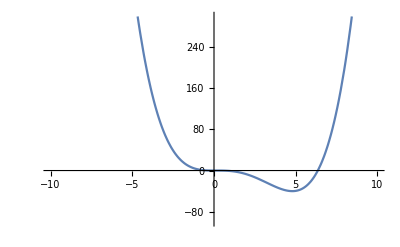

```mathematica
fn[x_]:=x^4/4-5*x^3/3+x^2/2
Plot[fn[x],{x,-10,10},PlotRange->{-100,300}]
```

```mathematica
(*bartab=Table[{i},{i,-10,10,0.1}];
Soln=NMinimize[{fn[x]-p*x,0≤x≤1},{x},Method->{"NelderMead","InitialPoints"->bartab}];
x14=x/.SolnL4[[2]];*)
```

```mathematica
LegendreTransform[fn[#] &]
LegendreTransform[Log[#] &]
```

```mathematica
ConditionalExpression[0, (205+44 √22+27 #1>0&&205+27 #1<44 √22)||205+27 #1>44 √22||205+44 √22+27 #1<0]&
```

1-Log[1/#1]&

```mathematica
L=100;
bartab=Table[{i},{i,-L,L,0.01}];
u[y_]:=x/.NMinimize[{fn[x]-y*x},{x},Method->{"NelderMead","InitialPoints"->bartab}][[2]]
g[y_]:=fn[u[y]]-u[y]*y
```

4.79129

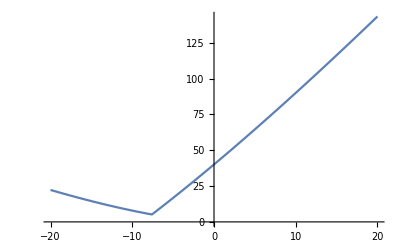

```mathematica
u[0]
Plot[-g[y],{y,-20,20}]
```